Entropy as a function of ‘p’, the relative enzymatic rate. As the rate of enzyme action compared with

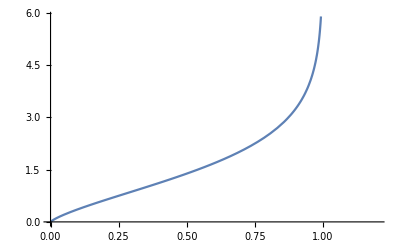

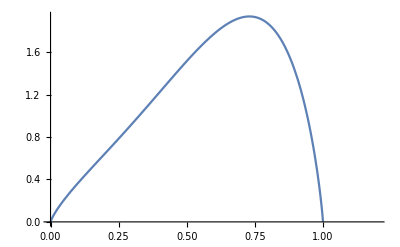

```mathematica
F[x_]:=-Log[1-x]-x/(1-x)*Log[x]
G[x_,L_]:=-Log[x]*((L-3)*x^(L-1)+2*x^L-L*x^(L+1)+x)/(1-x)-(1-x^L)*Log[1-x]
Plot[F[p],{p,0,1.2}]
Plot[G[p,4],{p,0,1.2}]
```

```mathematica
P[β_]:=1/(1+β)
En[β_]:=F@*P@β
Em[β_,L_]:=G[P[β],L]
Plot[En[β],{β,0,10}];
Plot[Em[β,4],{β,0,10}];
```

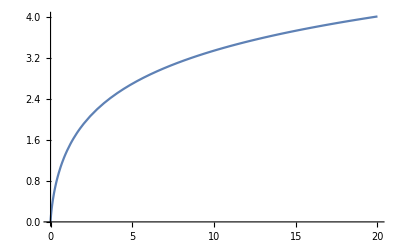

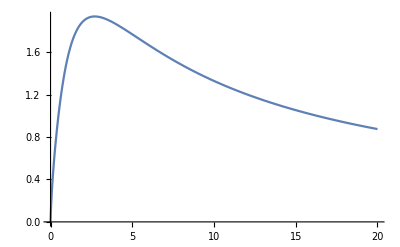

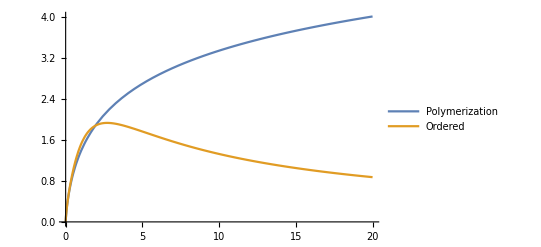

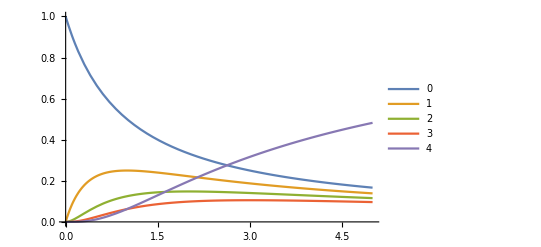

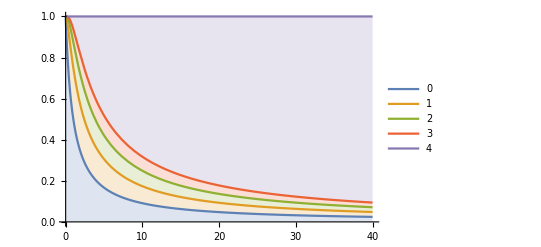

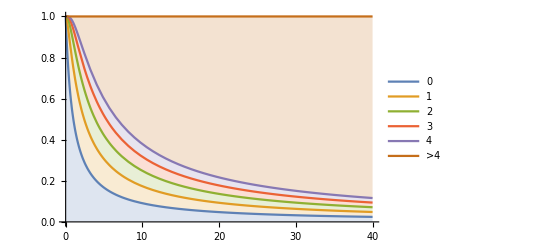

```mathematica
h[τ_]:=1/(1+1/τ)
En[τ_]:=F@*h@τ
Em[τ_,L_]:=G[h[τ],L]
Yn[τ_,l_]:=h[τ]^l(1-h[τ])
YL[τ_,L_]:=h[τ]^L

Plot[En[τ],{τ,0,20}]
Plot[Em[τ,4],{τ,0,20}]

Plot[{En[τ],Em[τ,4]}, {τ,0,20},PlotLegends->{"Polymerization","Ordered"}]

Plot[{Evaluate@Table[Yn[τ,l],{l,0,3}],YL[τ,4]},{τ,0,5},PlotRange->{0,1},PlotLegends->{"0","1","2","3","4"}]

P1=Evaluate@Table[1-YL[τ,L],{L,1,4}];
p2=Plot[{P1,1},{τ,0,40},PlotRange->{0,1} ,PlotLegends->{"0","1","2","3","4"}, Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4}}]

P1=Evaluate@Table[1-YL[τ,L],{L,1,5}];
p2=Plot[{P1,1},{τ,0,40},PlotRange->{0,1} ,PlotLegends->{"0","1","2","3","4",">4"}, Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4},6->{5}}]
```

```mathematica
Solve[h[τ]^4==1/20&&τ>0]
```

{{τ→Root[-1-4 #1-6 #1^2-4 #1^3+19 #1^4&,2]}}

```mathematica
Root[-1-4 #1-6 #1^2-4 #1^3+19 #1^4&,2]
```

Root[-1-4 #1-6 #1^2-4 #1^3+19 #1^4&,2]

```mathematica
Solve[Yn[τ,0]==1/20&&τ>0]
```

{{τ→19}}

```mathematica
Solve[Yn[τ,1]==1/20&&τ>0]
```

{{τ→9-4 √5},{τ→9+4 √5}}

```mathematica
Solve[Yn[τ,2]==1/20&&τ>0]
```

{{τ→Root[1+3 #1-17 #1^2+#1^3&,2]},{τ→Root[1+3 #1-17 #1^2+#1^3&,3]}}

```mathematica
Solve[Yn[τ,3]==1/20&&τ>0]
```

{{τ→Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,1]},{τ→Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,2]}}

```mathematica
Solve[Yn[τ,4]==1/20&&τ>0]
```

{{τ→Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2]},{τ→Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]}}

```mathematica
Solve[Yn[τ,5]==1/20&&τ>0]
```

{{τ→Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,1]},{τ→Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,2]}}

```mathematica
a[x_]:=1/;0.897068135363814<x
b[x_]:=0.2/; x<19
c[x_]:=0.4/;9-4 √5<x&&x<9+4 √5
d[x_]:=0.6/;Root[1+3 #1-17 #1^2+#1^3&,2]<x<Root[1+3 #1-17 #1^2+#1^3&,3]
e[x_]:=0.8/;Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,1]<x<Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,2]
f[x_]:=1/;Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2]<x<Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]
g[x_]:=1.2/;Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,1]<x<Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,2]
```

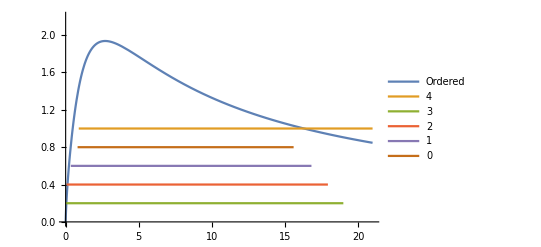

```mathematica
Plot[{Em[x,4],a[x],b[x],c[x],d[x],e[x]},{x,0,21},PlotRange->{0,2.2},PlotLegends->{"Ordered","4","3","2","1","0"}]
```

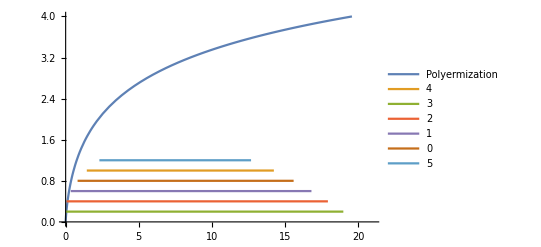

```mathematica
Plot[{En[x],f[x],b[x],c[x],d[x],e[x],g[x]},{x,0,21},PlotRange->{0,4},PlotLegends->{"Polyermization","4","3","2","1","0","5"}]
```